## Four-point Massive Exchange Correlation Function in de Sitter

This notebook contains the closed-form expression of the four-point correlation function of conformally coupled scalars mediated by the tree-level exchange of massive scalars. The expression is written in a single series form.

#### Analytical Expression

```mathematica
F3[z_, μ_]:= 1/Sqrt[2] Abs[Gamma[1/2+I μ]]^2 LegendreP[I μ-1/2, 0, 3, z]; (** F^{(3)} **);
F4pm[u_, v_, μ_]:=F3[1/u, μ] F3[1/v, μ]; (** F_{+-} **)
F4mp[u_, v_, μ_]:= Conjugate[F4pm[u, v, μ]]; (** F_{-+} **)
F4pp[u_, v_, μ_, nn_]:=
Module[{}, (** (1) labels correspond to |u|<|v|, and (2) labels correspond to |u|>|v| **)
A1 =   - F3[-1/u , μ] F3[1/v , μ];
A2 =   - F3[1/u , μ] F3[-1/v , μ];
B = -2/Pi Sum[(-1)^n (n+1)/((n+1)^2+μ^2) LegendreQ[n+1/2, 0, 3, 1/u]LegendreQ[n+1/2, 0, 3, 1/v], {n, 0, nn}];
B1 = 2/Pi Sum[(-1)^n (n+1)/((n+1)^2+μ^2) LegendreQ[n+1/2,  0, 3,1/u]LegendreQ[-n-3/2, 0, 3, 1/v], {n, 0, nn}];
B2 = 2/Pi Sum[(-1)^n (n+1)/((n+1)^2+μ^2) LegendreQ[n+1/2,  0, 3,1/v]LegendreQ[-n-3/2,  0, 3,1/u], {n, 0, nn}];
C1=  Sum[(-1)^n(n+1/2)/((n+1/2)^2+μ^2)((2n)!)/(2^(n-1)(n!)^2)LegendreQ[n, 0, 3, 1/u]/v^n Hypergeometric2F1[(1-n)/2, -n/2, 1/2-n, v^2],{n, 0, nn}];
C2=  Sum[(-1)^n(n+1/2)/((n+1/2)^2+μ^2)((2n)!)/(2^(n-1)(n!)^2)LegendreQ[n, 0, 3, 1/v]/u^n Hypergeometric2F1[(1-n)/2, -n/2, 1/2-n, u^2],{n, 0, nn}];
B+(A1+B1+C1)HeavisideTheta[v-u] + (A2+B2+C2)HeavisideTheta[u-v]
];
F4mm[u_, v_, μ_, nn_]:= Conjugate[F4pp[u, v, μ, nn]];
f[u_, v_, μ_, nn_]:= F4pp[u, v, μ, nn]+F4mm[u, v, μ, nn]+F4pm[u, v, μ]+F4mp[u, v, μ];
```

#### Figure μ = 1

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12}
```

{FontFamily→Latin Modern Roman,FontSize→12}

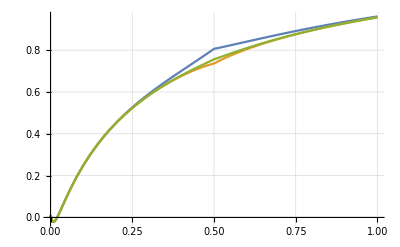

```mathematica
Plot[{f[u, v=0.5, μ=1, nn=2], f[u, v=0.5, μ=1, nn=5], f[u, v=0.5, μ=1, nn=10]}, {u, 0, 1}, AxesLabel->{MaTeX["u",Magnification->1.5], MaTeX["F(u, 0.5)",Magnification->1.5]}, PlotRange->Full, GridLines->Automatic, PlotLegends->{MaTeX["n=2",Magnification->1.5], MaTeX["n=5",Magnification->1.5], MaTeX["n=10",Magnification->1.5]}]
```

```mathematica
umin=0.0001;
umax=0.9999;
du=10^-3;
fμ1nn2=Table[{u,Re[f[u,v=0.5,μ=1,nn=2]]},{u,umin,umax,du}];
Export["/Users/deniswerth/Desktop/SpectralRepresentation/fμ1nn2.csv",fμ1nn2,"CSV"] 
fμ1nn5=Table[{u,Re[f[u,v=0.5,μ=1,nn=5]]},{u,umin,umax,du}];
Export["/Users/deniswerth/Desktop/SpectralRepresentation/fμ1nn5.csv",fμ1nn5,"CSV"] 
fμ1nn10=Table[{u,Re[f[u,v=0.5,μ=1,nn=10]]},{u,umin,umax,du}];
Export["/Users/deniswerth/Desktop/SpectralRepresentation/fμ1nn10.csv",fμ1nn10,"CSV"]
```

/Users/deniswerth/Desktop/SpectralRepresentation/fμ1nn2.csv

/Users/deniswerth/Desktop/SpectralRepresentation/fμ1nn5.csv

/Users/deniswerth/Desktop/SpectralRepresentation/fμ1nn10.csv

#### Figure μ = 2

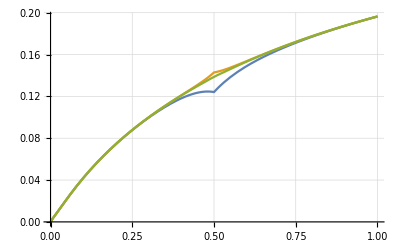

```mathematica
Plot[{f[u, v=0.5, μ=2, nn=5], f[u, v=0.5, μ=2, nn=10], f[u, v=0.5, μ=2, nn=30]}, {u, 0, 1}, AxesLabel->{MaTeX["u",Magnification->1.5], MaTeX["F(u, 0.5)",Magnification->1.5]}, PlotRange->Full, GridLines->Automatic, PlotLegends->{MaTeX["n=5",Magnification->1.5], MaTeX["n=10",Magnification->1.5], MaTeX["n=30",Magnification->1.5]}]
```

```mathematica
umin=0.0001;
umax=0.9999;
du=10^-3;
fμ2nn5=Table[{u,Re[f[u,v=0.5,μ=2,nn=5]]},{u,umin,umax,du}];
Export["/Users/deniswerth/Desktop/SpectralRepresentation/fμ2nn5.csv",fμ2nn5,"CSV"] 
fμ2nn10=Table[{u,Re[f[u,v=0.5,μ=2,nn=10]]},{u,umin,umax,du}];
Export["/Users/deniswerth/Desktop/SpectralRepresentation/fμ2nn10.csv",fμ2nn10,"CSV"] 
fμ2nn30=Table[{u,Re[f[u,v=0.5,μ=2,nn=30]]},{u,umin,umax,du}];
Export["/Users/deniswerth/Desktop/SpectralRepresentation/fμ2nn30.csv",fμ2nn30,"CSV"]
```

/Users/deniswerth/Desktop/SpectralRepresentation/fμ2nn5.csv

/Users/deniswerth/Desktop/SpectralRepresentation/fμ2nn10.csv

/Users/deniswerth/Desktop/SpectralRepresentation/fμ2nn30.csv